# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2025\PCS\Entropy

```mathematica
Get["D:\\INVESTIGACION\\2025\\PCS\\Entropy\\packages\\QMB - Copy.wl"]
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
Needs["MaTeX`"];
```

# Method

## Random product state

```mathematica
L=8;
hx=0.05;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
random=RandomChainProductState[L];
```

```mathematica
tlist=Range[0,1000,1];
```

```mathematica
randomt=Table[StateEvolution[t,random,eigenval,eigenvec],{t,tlist}];
```

```mathematica
densityrandomt=ParallelTable[Dyad[i,i],{i,randomt}];
```

```mathematica
reducedrandomt=Table[MatrixPartialTrace[i,2,{2^(L/2),2^(L/2)}],{i,densityrandomt}];
```

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
```

```mathematica
eigenreducedrandomt=ParallelTable[Sort[Eigenvalues[Chop[i]]],{i,reducedrandomt}];
```

```mathematica
entropies=ParallelTable[Total[Map[VNentropy,i]],{i,eigenreducedrandomt}];
```

```mathematica
ListPlot[{Transpose[{tlist,Chop[entropies]}],Transpose[{tlist,ConstantArray[Mean[Chop[entropies]],Length[tlist]]}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = 0.1 , Random product state",20,Black],PlotStyle->{Brown,Directive[Gray,Dashed]},ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All]
```

## Eigenvectors for h = 0

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
L=8;
hx=0.11;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

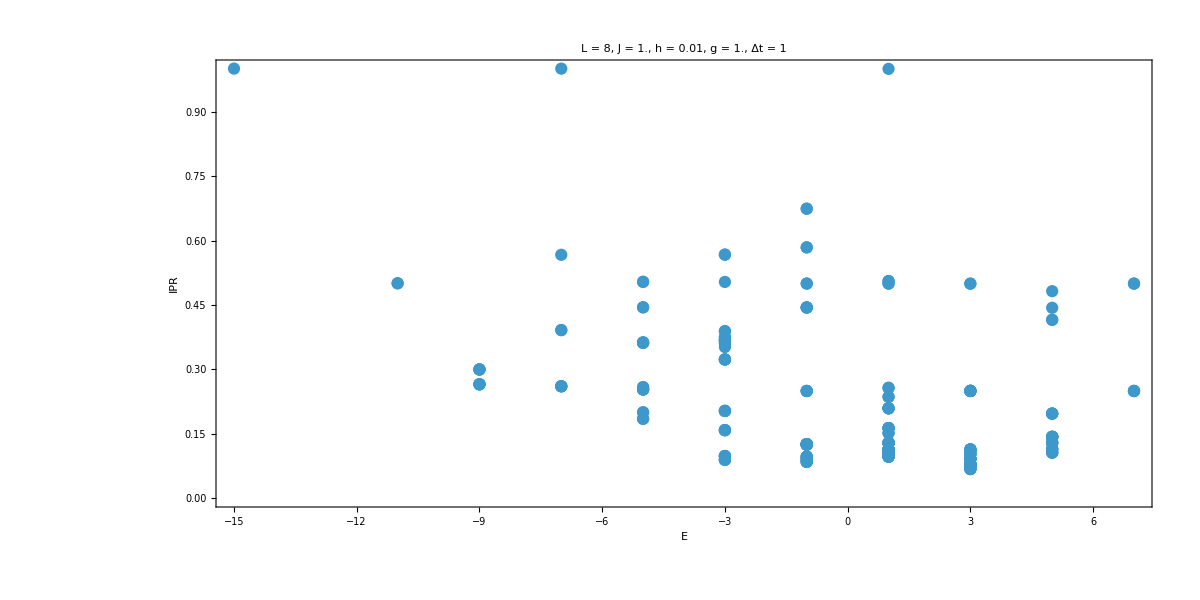

```mathematica
ListPlot[Transpose[{Sort[energytest],iprtestb}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["IPR"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All]
```

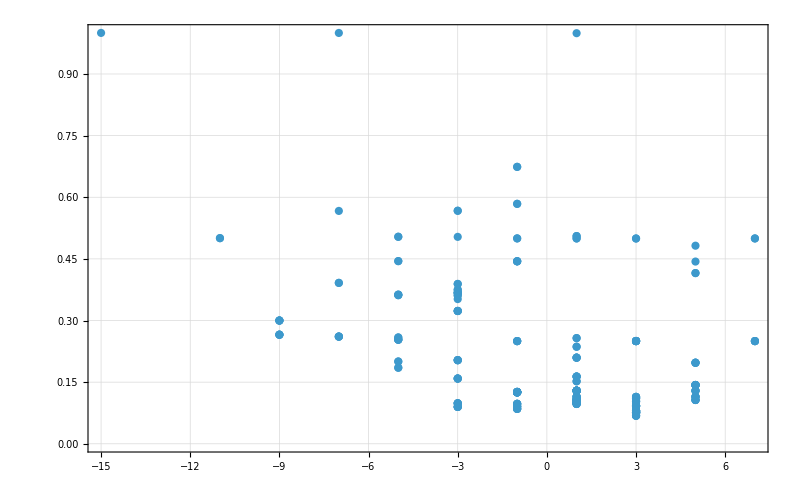

```mathematica
energytest=ParallelTable[Chop[i.H.i],{i,eigenvectest}];
sortedEigenvectors=SortBy[Transpose[{energytest,eigenvectest}],First][[All,2]];
basischangeb=ParallelTable[Conjugate[eigenvec].i,{i,sortedEigenvectors}];
iprtestb=ParallelTable[Total[Abs[i]^4],{i,basischangeb}];
ListPlot[Transpose[{Sort[energytest],iprtestb}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800]
```

```mathematica
data=Transpose[{Sort[energytest],iprtestb}];
uniqueElements=DeleteDuplicatesBy[data,First];
colors=Table[RGBColor[0.8(i/Length[uniqueElements]),0.5(1-i/Length[uniqueElements]),1-i/Length[uniqueElements]],{i,Length[uniqueElements]}]
index=DeleteDuplicatesBy[MapIndexed[{First[#1],First[#2]}&,data],First][[All,2]]
```

{RGBColor[0.1, 0.4375, Rational[7, 8]],RGBColor[0.2, 0.375, Rational[3, 4]],RGBColor[0.30000000000000004, 0.3125, Rational[5, 8]],RGBColor[0.4, 0.25, Rational[1, 2]],RGBColor[0.5, 0.1875, Rational[3, 8]],RGBColor[0.6000000000000001, 0.125, Rational[1, 4]],RGBColor[0.7000000000000001, 0.0625, Rational[1, 8]],RGBColor[0.8, 0., 0]}

{1,2,4,10,16,28,46,60}

## Eigenvectors for h = 0

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
```

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
L=8;
hx=0.1;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
tlist=Range[0,100,0.1];
```

```mathematica
test=Table[sortedEigenvectors[[i]],{i,index}];
```

```mathematica
colors1=Table[RGBColor[0.8(i/Length[test]),0.5(1-i/Length[test]),1-i/Length[test]],{i,Length[test]}]
```

{RGBColor[0.07272727272727274, 0.45454545454545453, Rational[10, 11]],RGBColor[0.14545454545454548, 0.4090909090909091, Rational[9, 11]],RGBColor[0.21818181818181817, 0.36363636363636365, Rational[8, 11]],RGBColor[0.29090909090909095, 0.3181818181818182, Rational[7, 11]],RGBColor[0.36363636363636365, 0.2727272727272727, Rational[6, 11]],RGBColor[0.43636363636363634, 0.22727272727272727, Rational[5, 11]],RGBColor[0.5090909090909091, 0.18181818181818182, Rational[4, 11]],RGBColor[0.5818181818181819, 0.13636363636363635, Rational[3, 11]],RGBColor[0.6545454545454547, 0.09090909090909091, Rational[2, 11]],RGBColor[0.7272727272727273, 0.045454545454545456, Rational[1, 11]],RGBColor[0.8, 0., 0]}

```mathematica
eigenvect=ParallelTable[StateEvolution[t,j,eigenval,eigenvec],{j,test},{t,tlist}];
```

```mathematica
densityrandomt=Table[Dyad[eigenvect[[j,i]],eigenvect[[j,i]]],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
reducedrandomt=Table[MatrixPartialTrace[densityrandomt[[j,i]],2,{2^(L/2),2^(L/2)}],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
eigenreducedrandomt=ParallelTable[Sort[Eigenvalues[Chop[reducedrandomt[[j,i]]]]],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
entropies=ParallelTable[Total[Chop[Map[VNentropy,eigenreducedrandomt[[j,i]]]]],{j,Length[test]},{i,Length[tlist]}];
```

```mathematica
data=Table[Transpose[{tlist,i}],{i,entropies}];
```

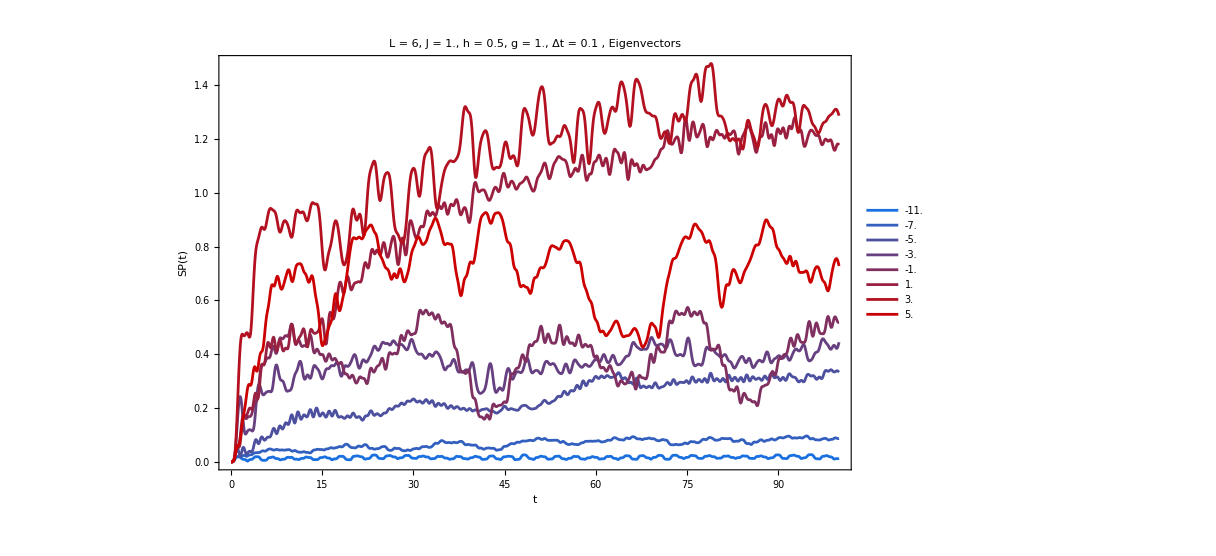

```mathematica
ListPlot[data,PlotTheme->"Detailed",PlotStyle->colors,Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = 0.1 , Eigenvectors",20,Black],ImageSize->900,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All,PlotLegends->uniqueElements[[All,1]]]
```

## Single Eigenvector for h = 0

```mathematica
q=8;
index[[q]]
```

60

```mathematica
test={sortedEigenvectors[[1]],sortedEigenvectors[[-1]]};
```

```mathematica
eigenvect=ParallelTable[StateEvolution[t,j,eigenval,eigenvec],{j,test},{t,tlist}];
densityrandomt=Table[Dyad[eigenvect[[j,i]],eigenvect[[j,i]]],{j,Length[test]},{i,Length[tlist]}];
reducedrandomt=Table[MatrixPartialTrace[densityrandomt[[j,i]],2,{2^(L/2),2^(L/2)}],{j,Length[test]},{i,Length[tlist]}];
eigenreducedrandomt=ParallelTable[Sort[Eigenvalues[Chop[reducedrandomt[[j,i]]]]],{j,Length[test]},{i,Length[tlist]}];
entropies=ParallelTable[Total[Chop[Map[VNentropy,eigenreducedrandomt[[j,i]]]]],{j,Length[test]},{i,Length[tlist]}];
data=Table[Transpose[{tlist,i}],{i,entropies}];
```

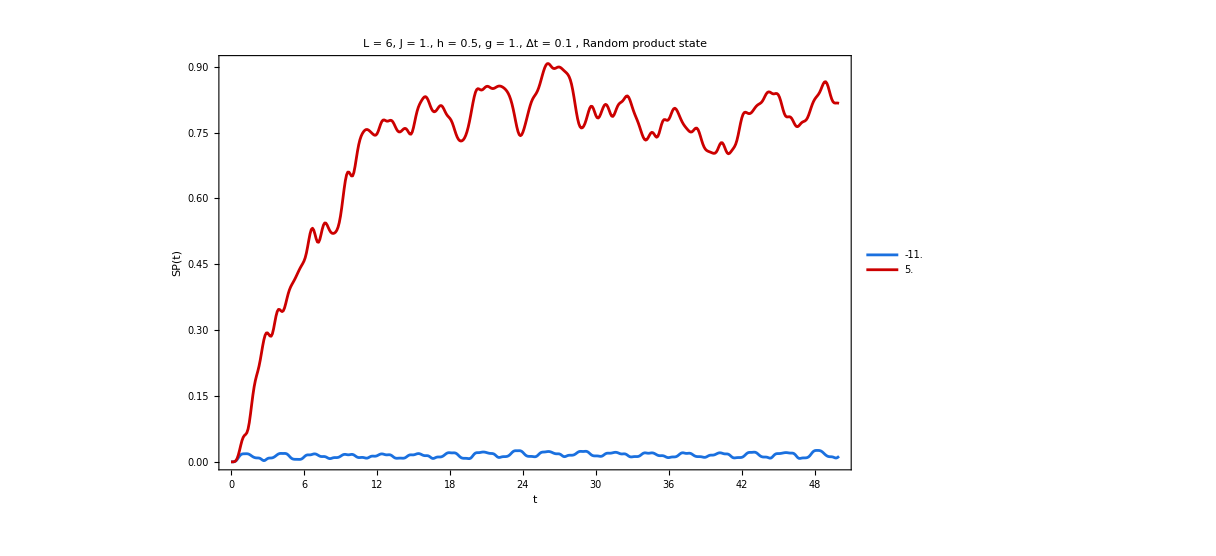

```mathematica
ListPlot[data,PlotTheme->"Detailed",PlotStyle->{colors[[1]],colors[[-1]]},Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = 0.1 , Random product state",20,Black],ImageSize->900,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All,PlotLegends->{uniqueElements[[All,1]][[1]],uniqueElements[[All,1]][[-1]]}]
```

```mathematica
data//Dimensions
```

{2,501,2}

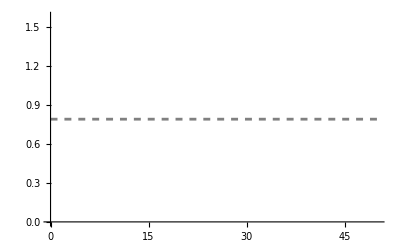

```mathematica
mean=Plot[Mean[data[[2]][[All,2]][[100;;-1]]],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Gray,Dashed]]
```

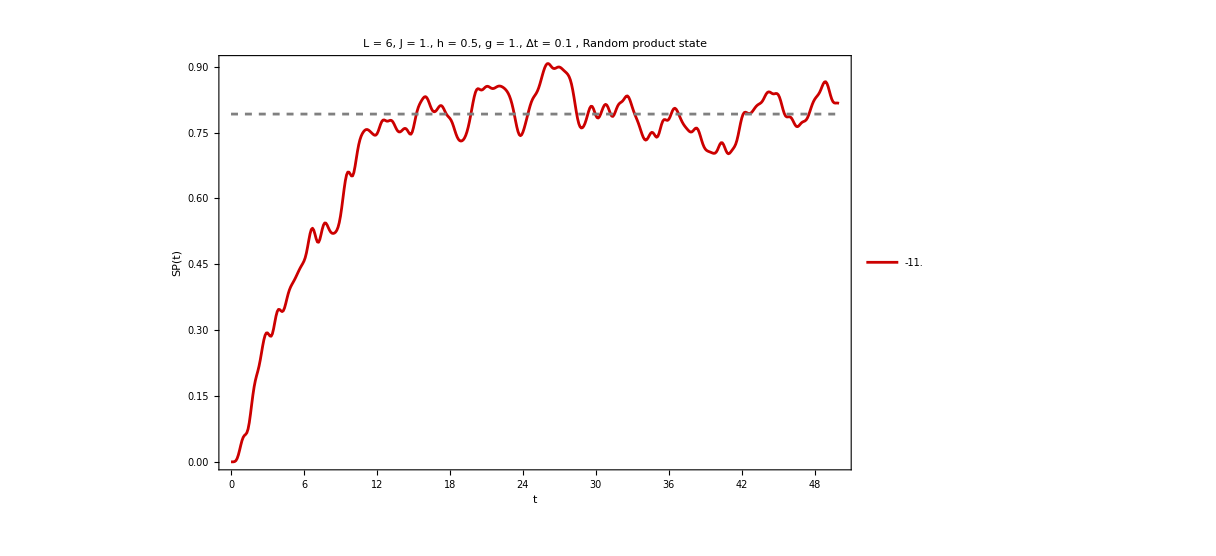

```mathematica
Show[{ListPlot[data[[-1]],PlotTheme->"Detailed",PlotStyle->{colors[[1]],colors[[-1]]},Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = 0.1 , Random product state",20,Black],ImageSize->900,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All,PlotLegends->{uniqueElements[[All,1]][[1]],uniqueElements[[All,1]][[-1]]}],mean},PlotRange->All]
```

# All together

## Random product state

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state,state],2,{2^(L/2),2^(L/2)}];
purity=Tr[rho.rho];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],Chop[1-purity]}
];
```

```mathematica
L=6;
(*Transverse B field*)
h=1.0;
(*Interaction*)
J=1.;
(*Parallel B field*)
g=1.0;
(*Hamiltonian*)
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
```

```mathematica
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif)
```

0.012339

```mathematica
random=RandomChainProductState[L];
```

```mathematica
tlist=Range[0,(10^3),Δt];
tlist//Length
```

81044

```mathematica
entropies=ParallelTable[{t,svn[random,t]},{t,tlist},DistributedContexts->Full];
```

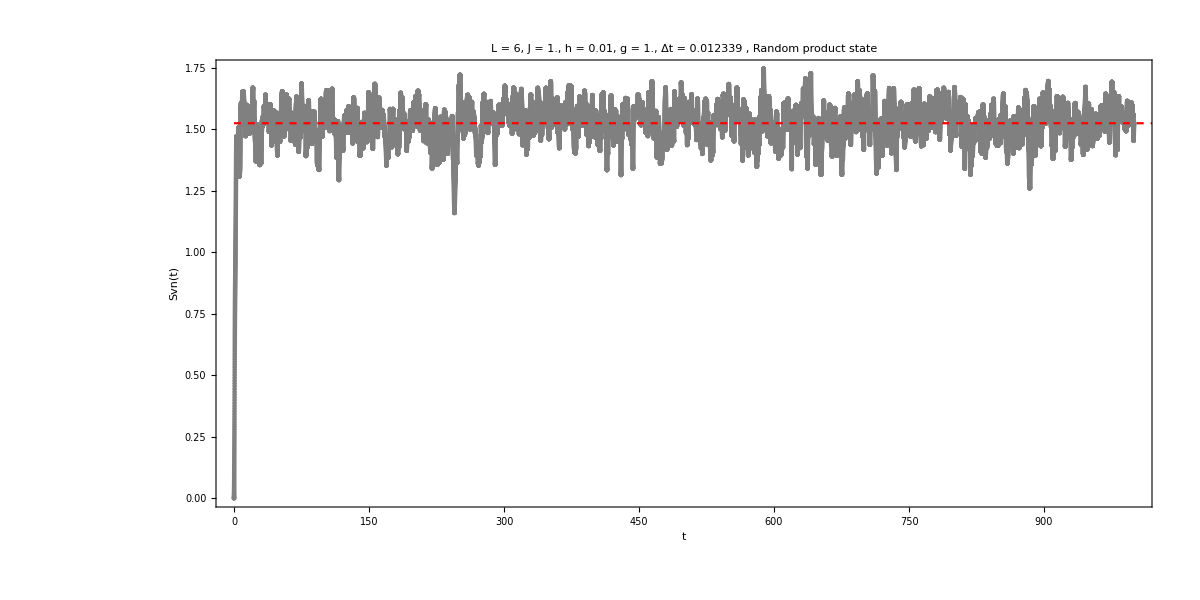

```mathematica
Show[ListPlot[entropies,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Gray,Dashed],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All],Plot[Mean[entropies],{x,0,Length[tlist]},PlotStyle->Directive[Dashed,Red]],AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Export["entropyb_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[hx]<>".m",entropies]
```

entropyb_randomstate_L_8_g_1._h_0.01.m

```mathematica
plus={};
minus={};
mean=Mean[entropies[[All,2]]];
Table[If[entropies[[i,2]]<mean&&entropies[[i+1,2]]>mean,AppendTo[plus,tlist[[i]]]],{i,Length[entropies]-1}];
Table[If[entropies[[i,2]]>mean&&entropies[[i+1,2]]<mean,AppendTo[minus,tlist[[i]]]],{i,Length[entropies]-1}];
Export["uptimesb_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[hx]<>".m",plus]
Export["downtimesb_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[hx]<>".m",minus]
```

uptimesb_randomstate_L_8_g_1._h_0.01.m

downtimesb_randomstate_L_8_g_1._h_0.01.m

```mathematica
plus//Length
Mean[Differences[plus]]//N
StandardDeviation[Differences[plus]]//N
minus//Length
Mean[Differences[minus]]//N
StandardDeviation[Differences[minus]]//N
```

2622

4.07669

2.26267

2621

4.07748

2.26274

```mathematica
hlist=Range[0.05,1,0.05];
```

```mathematica
Do[

Clear[eigenval,eigenvec];
H=IsingNNOpenHamiltonian[h,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
entropies=ParallelTable[{t,svn[random,t]},{t,tlist},DistributedContexts->Full];
Export["entropy_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[h]<>".m",entropies];
plus={};
minus={};
mean=Mean[entropies[[All,2]]];
Table[If[entropies[[i,2]]<mean&&entropies[[i+1,2]]>mean,AppendTo[plus,tlist[[i]]]],{i,Length[entropies]-1}];
Table[If[entropies[[i,2]]>mean&&entropies[[i+1,2]]<mean,AppendTo[minus,tlist[[i]]]],{i,Length[entropies]-1}];
Export["uptimes_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[h]<>".m",plus];
Export["downtimes_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[h]<>".m",minus];

,{h,hlist}];
```

```mathematica
allentropies=Table[Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Entropy\\entropy_randomstate_L_8_g_1._h_"<>ToString[h]<>".m"],{h,hlist}];
```

```mathematica
allplots=Table[Show[ListPlot[allentropies[[i]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[i]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Gray,Dashed],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All],Plot[Mean[allentropies[[i]]],{x,0,Length[tlist]},PlotStyle->Directive[Dashed,Red]],AspectRatio->1/2,ImageSize->1200],{i,Length[allentropies]}];
```

```mathematica
Table[Export["entropy_randomstate_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[hlist[[i]]]<>".png",allplots[[i]],ImageResolution->400],{i,Length[hlist]}]
```

{entropy_randomstate_L_8_g_1._h_0.05.png,entropy_randomstate_L_8_g_1._h_0.1.png,entropy_randomstate_L_8_g_1._h_0.15.png,entropy_randomstate_L_8_g_1._h_0.2.png,entropy_randomstate_L_8_g_1._h_0.25.png,entropy_randomstate_L_8_g_1._h_0.3.png,entropy_randomstate_L_8_g_1._h_0.35.png,entropy_randomstate_L_8_g_1._h_0.4.png,entropy_randomstate_L_8_g_1._h_0.45.png,entropy_randomstate_L_8_g_1._h_0.5.png,entropy_randomstate_L_8_g_1._h_0.55.png,entropy_randomstate_L_8_g_1._h_0.6.png,entropy_randomstate_L_8_g_1._h_0.65.png,entropy_randomstate_L_8_g_1._h_0.7.png,entropy_randomstate_L_8_g_1._h_0.75.png,entropy_randomstate_L_8_g_1._h_0.8.png,entropy_randomstate_L_8_g_1._h_0.85.png,entropy_randomstate_L_8_g_1._h_0.9.png,entropy_randomstate_L_8_g_1._h_0.95.png,entropy_randomstate_L_8_g_1._h_1..png}

```mathematica
datap={};
datam={};
meanentropies={};
Do[

plus={};
minus={};
mean=Mean[allentropies[[j]][[All,2]]];
Table[If[allentropies[[j]][[i,2]]<=mean&&allentropies[[j]][[i+1,2]]>mean,AppendTo[plus,tlist[[i]]]],{i,Length[allentropies[[1]]]-1}];
Table[If[allentropies[[j]][[i,2]]>=mean&&allentropies[[j]][[i+1,2]]<mean,AppendTo[minus,tlist[[i]]]],{i,Length[allentropies[[1]]]-1}];
AppendTo[meanentropies,Transpose[{hlist[[j]],mean}]];
AppendTo[datap,Transpose[{hlist[[j]],Mean[Differences[plus]],StandardDeviation[Differences[plus]]}]];
AppendTo[datam,Transpose[{hlist[[j]],Mean[Differences[minus]],StandardDeviation[Differences[minus]]}]];

,{j,Length[allentropies]}];
```

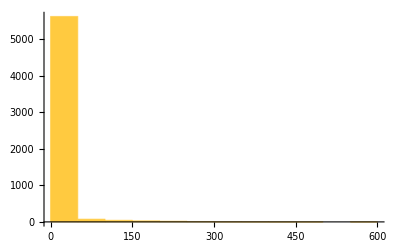

8.03217

29.1993

```mathematica
Histogram[Differences[plus]]
Differences[plus]//Mean//N
Differences[plus]//StandardDeviation//N
```

## Open boundary conditions

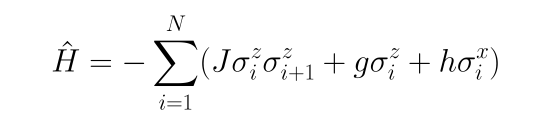

-Graphics-

-Graphics-

-Graphics-

```mathematica
Matex
```

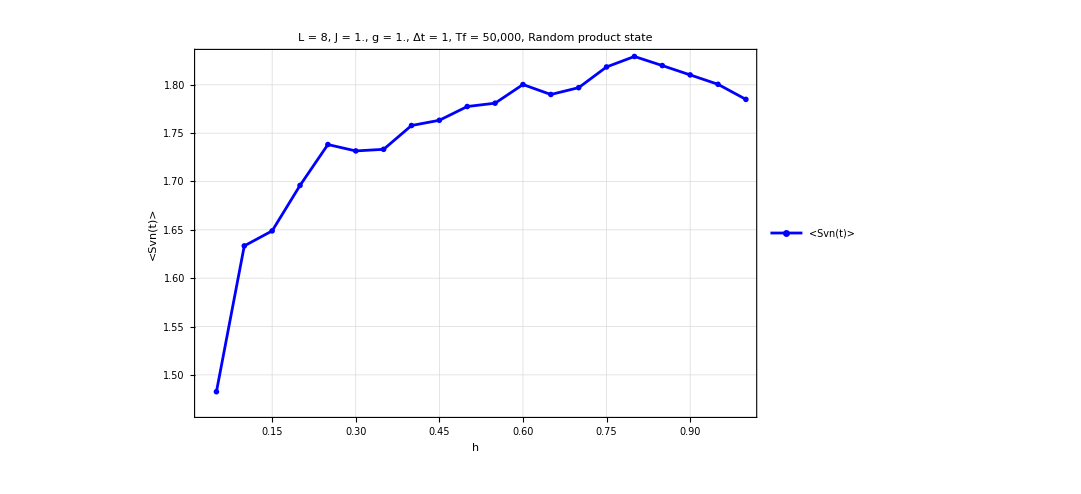

```mathematica
ListPlot[meanentropies,PlotRange->All,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>", Tf = 50,000, Random product state",20,Black],PlotTheme->"Detailed",FrameLabel->{Style["h"],Style["<Svn(t)>"]},FrameStyle->Directive[Black,FontSize->30],ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{Blue},PlotLegends->{"<Svn(t)>"}]
```

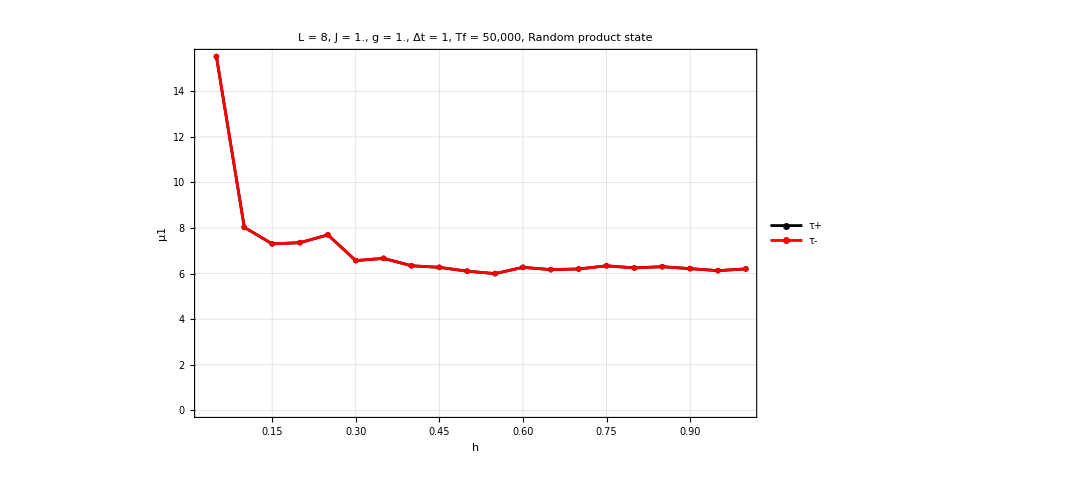

```mathematica
ListPlot[{Transpose[{datap[[All,1]],datap[[All,2]]}],Transpose[{datam[[All,1]],datam[[All,2]]}]},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>", Tf = 50,000, Random product state",20,Black],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["h"],Style["μ1"]},FrameStyle->Directive[Black,FontSize->30],ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{Black,Red},PlotLegends->{"τ+","τ-"}]
```

μ2 = std = (1/(n-1)∑_(i=1)^n (x_i-μ̂ 1)^2)^(1/2)

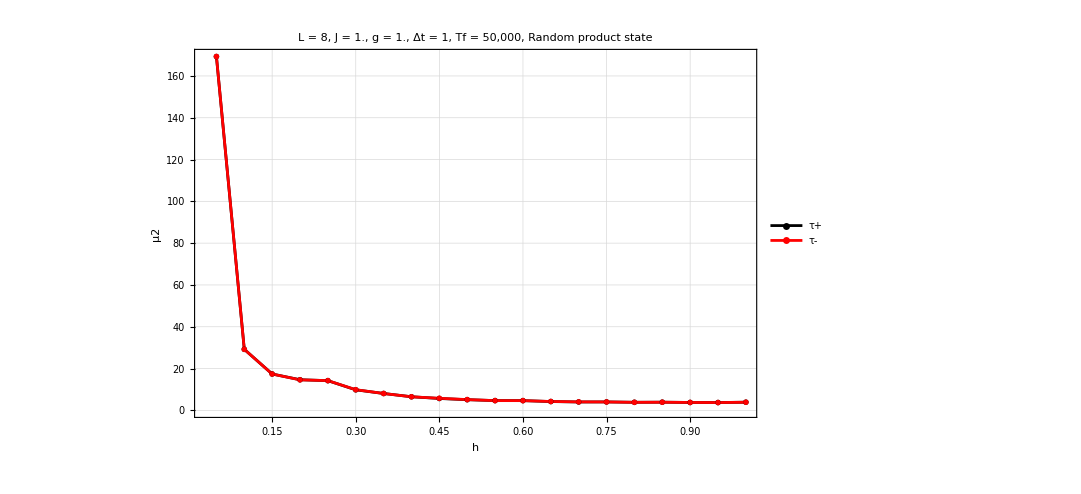

```mathematica
ListPlot[{Transpose[{datap[[All,1]],datap[[All,3]]}],Transpose[{datam[[All,1]],datam[[All,3]]}]},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>", Tf = 50,000, Random product state",20,Black],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["h"],Style["μ2"]},FrameStyle->Directive[Black,FontSize->30],ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{Black,Red},PlotLegends->{"τ+","τ-"}]
```

## Plots

```mathematica
ListPlot[Transpose[{Sort[energytest],iprtestb}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["IPR"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All]
```

-Graphics-

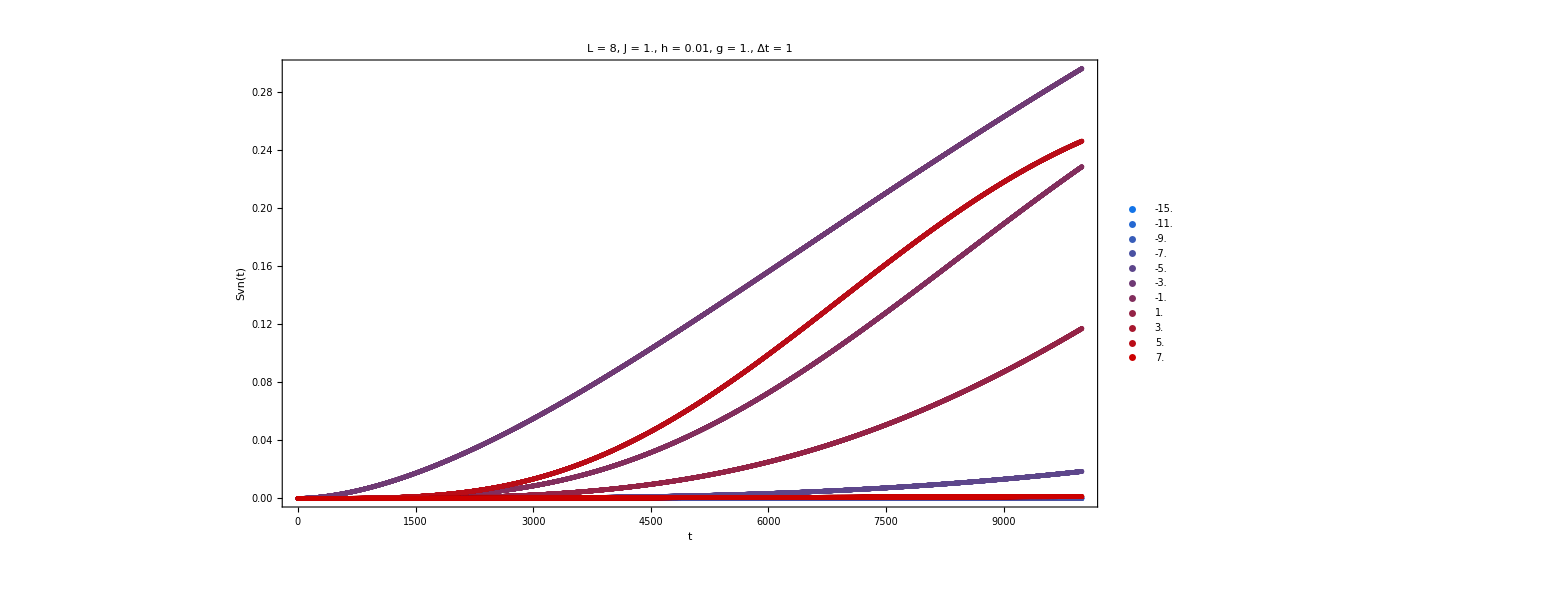

```mathematica
q=1;
ListPlot[allentropies[[q]][[All]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],PlotStyle->colors,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All,PlotLegends->uniques[[q]]]
```

```mathematica
ListPlot[Transpose[{Sort[energytest],iprtestb}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["IPR"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All]
```

-Graphics-

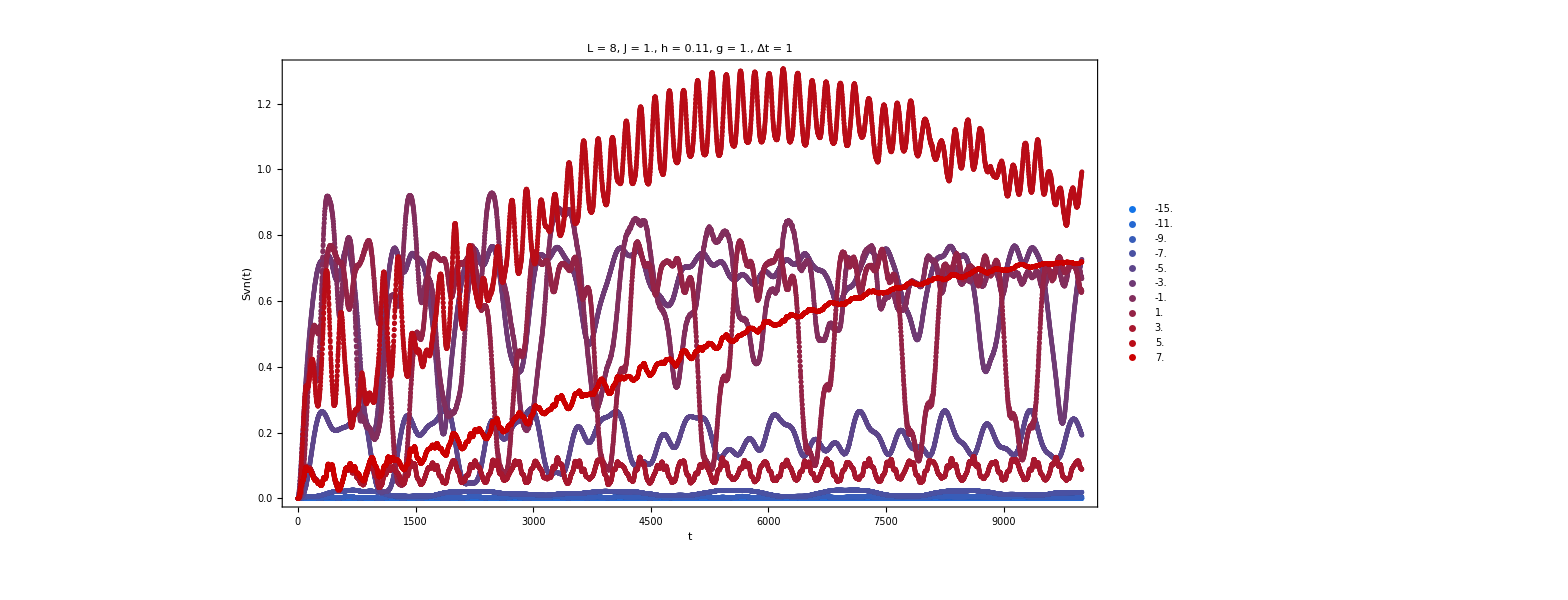

```mathematica
q=11;
ListPlot[allentropies[[q]][[All]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],PlotStyle->colors,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All,PlotLegends->uniques[[q]]]
```

## Infinite time entropy

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ},
rho=MatrixPartialTrace[Dyad[state,state],1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[smean];
smean[ini_]:=Module[{state=Dyad[ini,ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=6;
(*Transverse B field*)
h=1.0;
(*Interaction*)
J=1.;
(*Parallel B field*)
g=1.0;
(*Hamiltonian*)
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
```

```mathematica
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif)
```

0.012339

```mathematica
random=RandomChainProductState[L];
randomene=Conjugate[eigenvec].random;
```

```mathematica
tlist=Range[0,(10^3),Δt];
tlist//Length
```

81044

```mathematica
entropies=ParallelTable[{t,svn[random,t]},{t,tlist},DistributedContexts->Full];
```

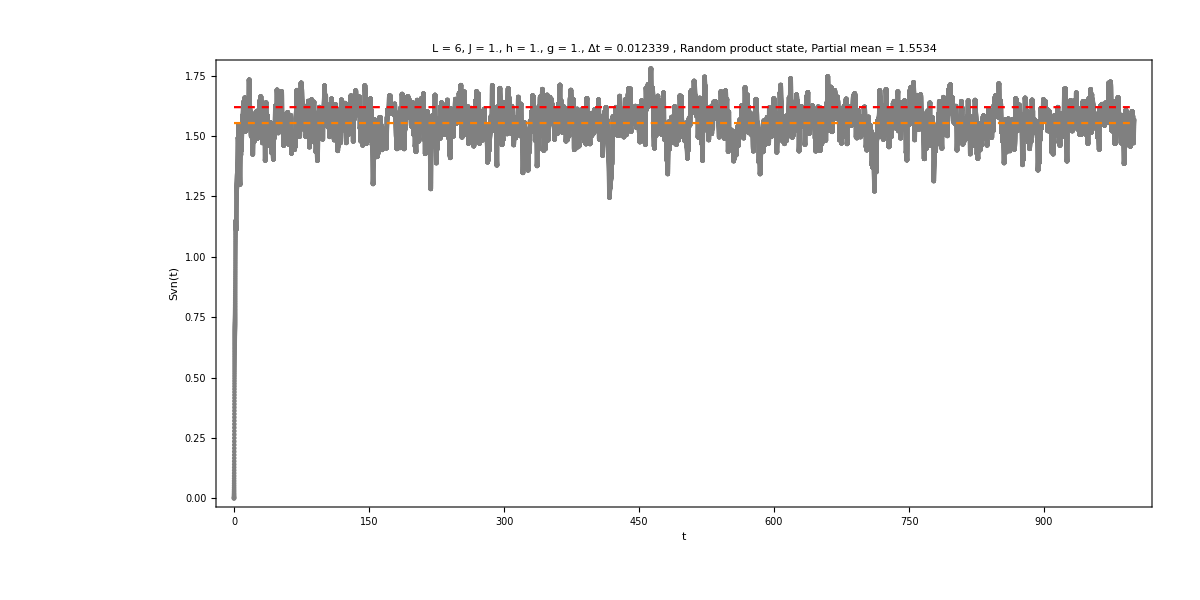

```mathematica
Show[ListPlot[entropies,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, Partial mean = "<>ToString[Mean[entropies[[All,2]]]],20,Black],PlotStyle->Directive[Gray,Dashed],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All],Plot[{Mean[entropies[[All,2]]],smean[randomene]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Orange],Directive[Dashed,Red]}],AspectRatio->1/2,ImageSize->1200,PlotRange->All]
```

# Several random states

## Open

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
```

```mathematica
L=6;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
```

```mathematica
tlist=Range[0,(10),Δt];
tlist//Length
```

811

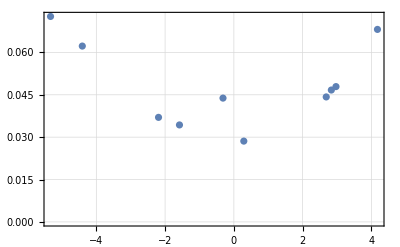

```mathematica
randoms=Table[RandomChainProductState[L],{i,10}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Table[Transpose[{tlist,entropies[[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,entropies[[i]][[All,2]]}],{i,Length[randoms]}];
```

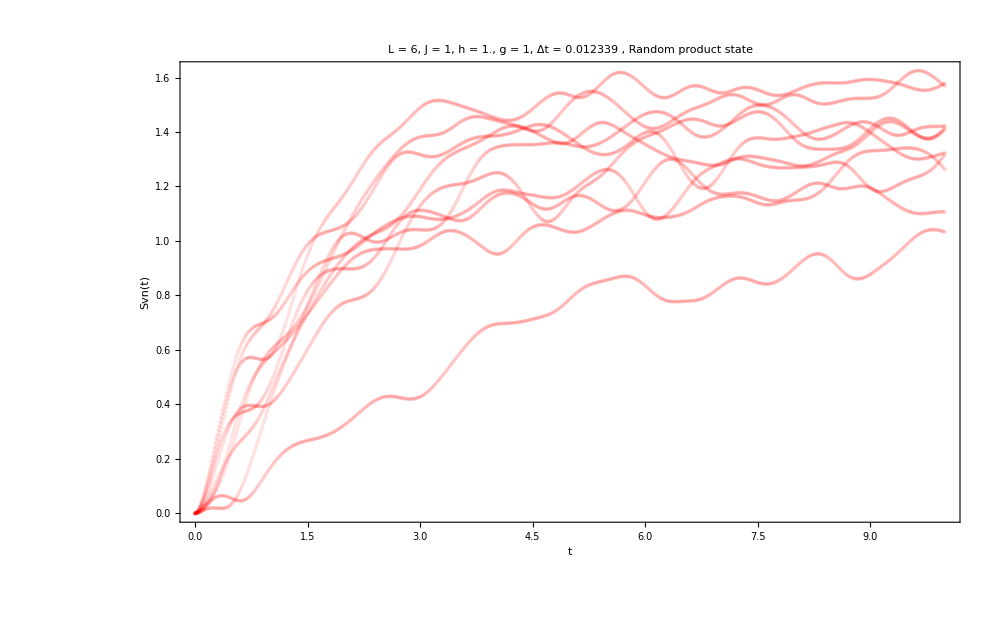

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Red,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

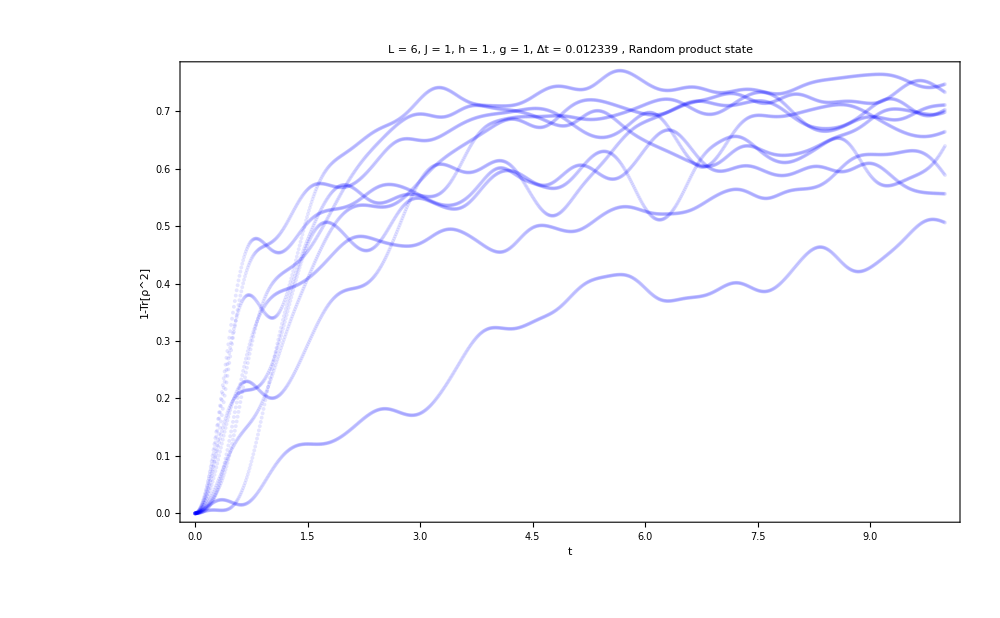

```mathematica
purityplots=ListPlot[entro2,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Blue,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["1-Tr[ρ^2]"]},PlotRange->All,ImageSize->1000]
```

## Closed

```mathematica
L=6;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
```

```mathematica
random=RandomChainProductState[L];
randomene=Conjugate[eigenvec].random;
```

```mathematica
tlist=Range[0,0.5(10^3),Δt];
tlist//Length
```

42422

```mathematica
randoms=Table[RandomChainProductState[L],{i,20}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
```

```mathematica
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
```

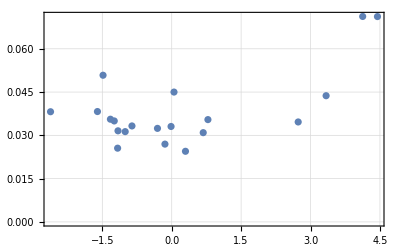

```mathematica
ListPlot[Transpose[{energies,iprs}],PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
entropies=ParallelTable[{t,svn[j,t]},{j,randoms},{t,tlist},DistributedContexts->Full];
```

```mathematica
ListPlot[entropies,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, Partial mean = "<>ToString[1.0],20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

```mathematica
means=Table[Mean[i],{i,entropies}];
```

```mathematica
ListPlot[means[[All,2]],PlotRange->All]
```

## Open coherent states

```mathematica
L=6;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
```

```mathematica
tlist=Range[0,(10^2),Δt];
tlist//Length
```

8105

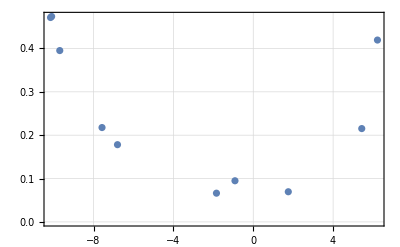

```mathematica
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Table[Transpose[{tlist,entropies[[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,entropies[[i]][[All,2]]}],{i,Length[randoms]}];
```

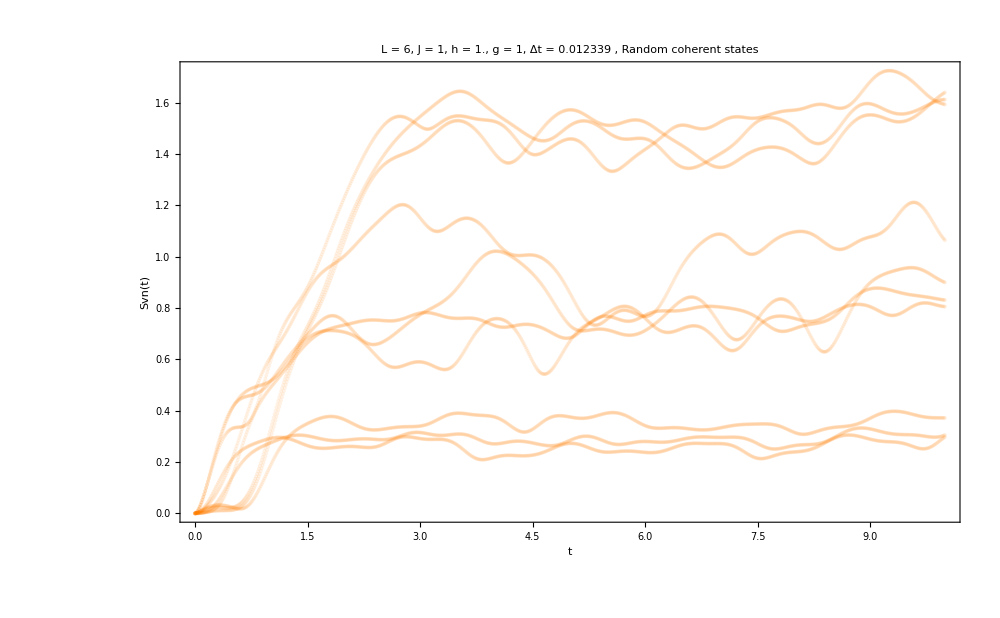

```mathematica
svnplotsb=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random coherent states",20,Black],PlotStyle->Directive[Orange,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

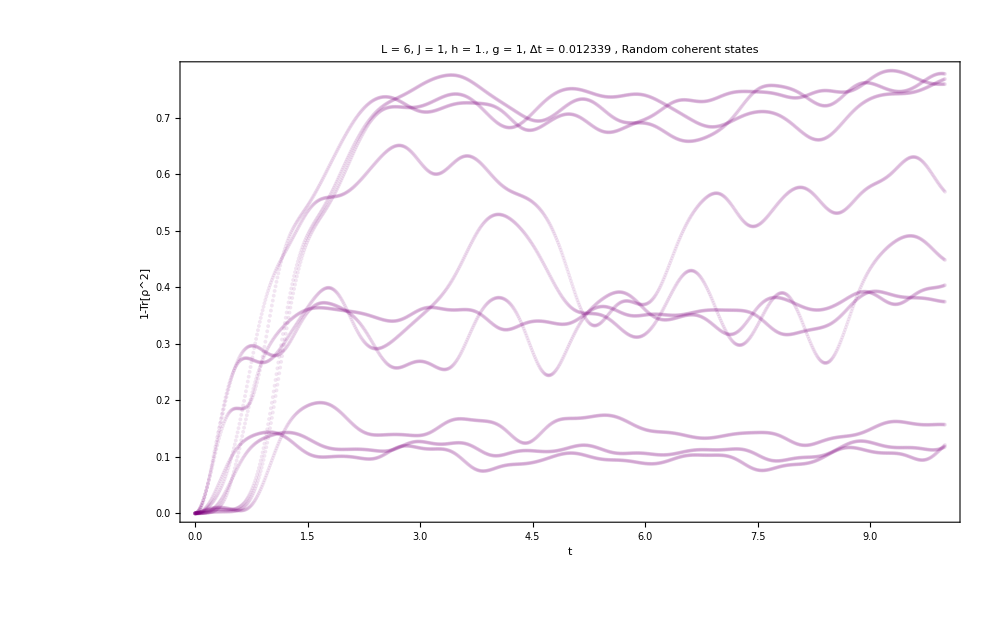

```mathematica
purityplotsb=ListPlot[entro2,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random coherent states",20,Black],PlotStyle->Directive[Purple,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["1-Tr[ρ^2]"]},PlotRange->All,ImageSize->1000]
```

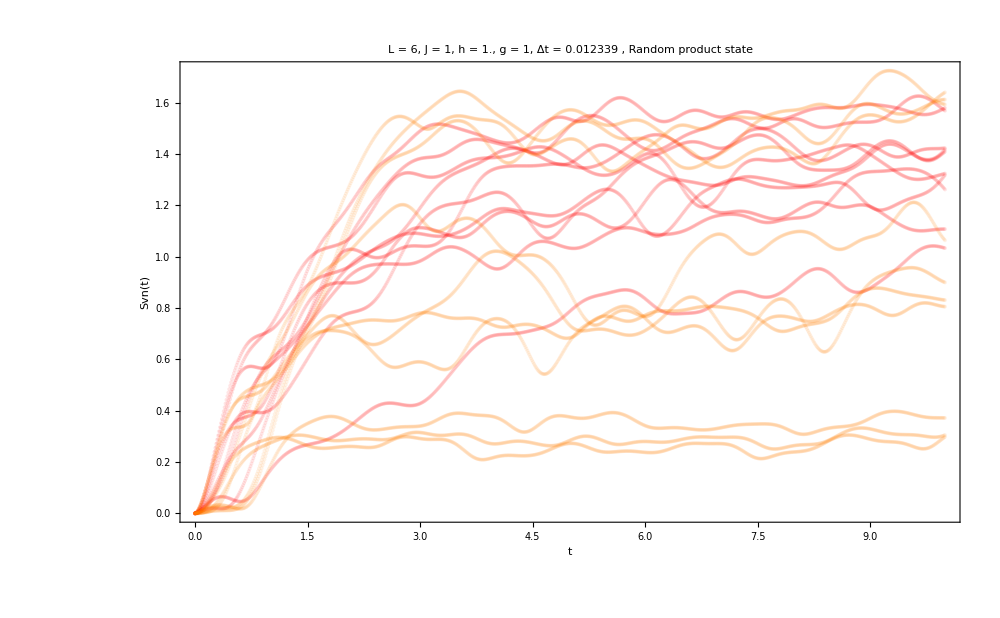

```mathematica
Show[{svnplots,svnplotsb},PlotRange->All]
```

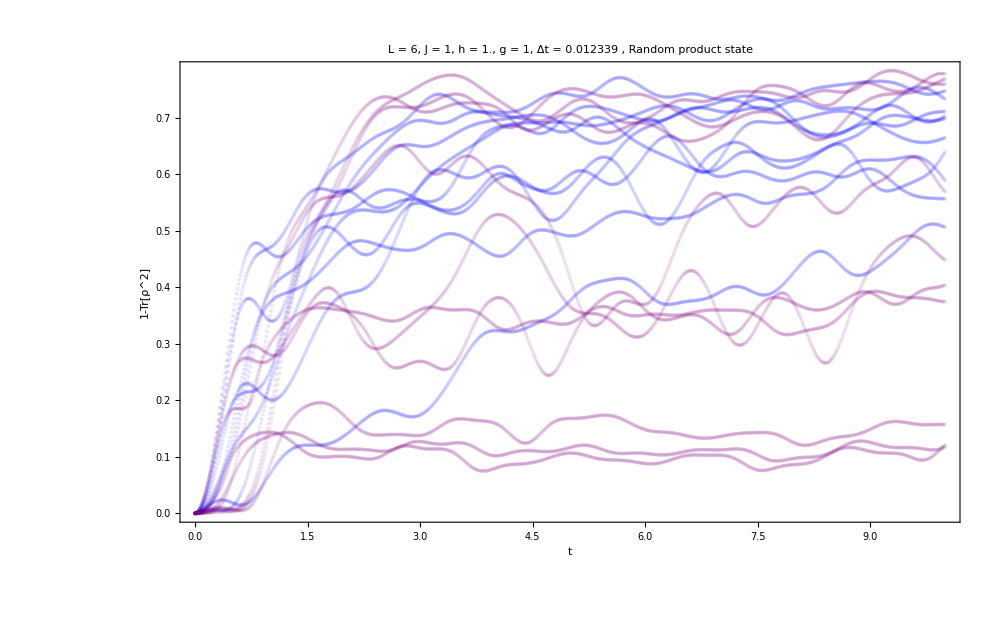

```mathematica
Show[{purityplots,purityplotsb},PlotRange->All]
```

## Calculation

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Tr[rho.rho];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-Chop[purity]}
];
```

```mathematica
Clear[h];
h=0.5;
```

```mathematica
L=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_4_openchain_10_randomcoherentstates_h_0.5.m",{randoms,entropies}];
```

```mathematica
L=4;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_4_closedchain_10_randomcoherentstates_h_0.5.m",{randoms,entropies}];
```

```mathematica
L=6;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_6_openchain_10_randomcoherentstates_h_0.5.m",{randoms,entropies}];
```

```mathematica
L=6;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_6_closedchain_10_randomcoherentstates_h_0.5.m",{randoms,entropies}];
```

```mathematica
L=8;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_8_openchain_10_randomcoherentstates_h_0.5.m",{randoms,entropies}];
```

```mathematica
L=8;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_8_closedchain_10_randomcoherentstates_h_0.5.m",{randoms,entropies}];
```

```mathematica
Clear[h];
h=1.0;
```

```mathematica
L=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_4_openchain_10_randomcoherentstates_h_1.m",{randoms,entropies}];
```

```mathematica
L=4;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_4_closedchain_10_randomcoherentstates_h_1.m",{randoms,entropies}];
```

```mathematica
L=6;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_6_openchain_10_randomcoherentstates_h_1.m",{randoms,entropies}];
```

```mathematica
L=6;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_6_closedchain_10_randomcoherentstates_h_1.m",{randoms,entropies}];
```

```mathematica
L=8;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
randoms=Table[coherentstate[RandomQubitState[],L],{i,10}];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_8_openchain_10_randomcoherentstates_h_1.m",{randoms,entropies}];
```

```mathematica
L=8;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
Export["entropies_withpurity_L_8_closedchain_10_randomcoherentstates_h_1.m",{randoms,entropies}];
```

# Results

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Tr[rho.rho];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-Chop[purity]}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
Clear[h,L];
h=0.5;
J=g=1;
```

```mathematica
L=8;
(*H=IsingNNOpenHamiltonian[h,g,J,L];*)
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
```

```mathematica
texts={"closed","open"};
text=texts[[1]];
Clear[data1];
```

```mathematica
data1=Import["D:\\INVESTIGACION\\2025\\PCS\\Entropy\\entropies_withpurity_L_"<>ToString[L]<>"_"<>ToString[text]<>"chain_10_randomstates_h_"<>ToString[h]<>".m"];
```

```mathematica
randoms=data1[[1]];
```

```mathematica
entro1=Table[Transpose[{tlist,data1[[2]][[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))data1[[2]][[i]][[All,2]]}],{i,Length[randoms]}];
```

```mathematica
meanssvn1=Table[Mean[i[[All,2]]],{i,entro1}];
meanspurity1=Table[Mean[i[[All,2]]],{i,entro2}];
diagonalentropies1=Table[sdiag[i],{i,randoms}];
```

```mathematica
fig1=ListPlot[{meanssvn1,diagonalentropies1},PlotTheme->"Detailed",Joined->True,PlotMarkers->Automatic,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" ,10 Random product state, "<>ToString[text]<>" chain",25,Black],PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},FrameLabel->{Style[MaTeX["i",FontSize->40],Black],Style[MaTeX["S",FontSize->40],Black]},FrameStyle->Directive[Black,FontSize->30],PlotRange->All,ImageSize->1000,PlotLegends->{Style[MaTeX["<S_{vn}>",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]}];
Export["entropycomparison_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>".png",fig1,ImageResolution->400]
```

entropycomparison_closedchain_L_8_h_0.5.png

```mathematica
Do[
svnplots1=Show[{ListPlot[entro1[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, "<>ToString[text]<>" chain",20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->40],Black],Style[MaTeX["S_{vn}(t)",FontSize->40],Black]},PlotRange->All,ImageSize->1000],Plot[{meanssvn1[[q]],diagonalentropies1[[q]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},PlotLegends->{Style[MaTeX["<S_{vn}>",FontSize->30],Black],Style[MaTeX["S_{d}",FontSize->30],Black]}]},PlotRange->All];
Export["vnentropy_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>"_state_"<>ToString[q]<>".png",svnplots1,ImageResolution->400];
,{q,10}]
```

```mathematica
Do[
svnplots1=Show[{ListPlot[entro2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, "<>ToString[text]<>" chain",20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->40],Black],Style[MaTeX["1- Tr(\\hat{\\rho}_{B}^2)",FontSize->40],Black]},PlotRange->All,ImageSize->1000],Plot[meanspurity1[[q]],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},PlotLegends->{Style[MaTeX["S_{l}",FontSize->30],Black]}]},PlotRange->All];
Export["purity_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>"_state_"<>ToString[q]<>".png",svnplots1,ImageResolution->400];
,{q,10}]
```